Single Wavelength IFAC

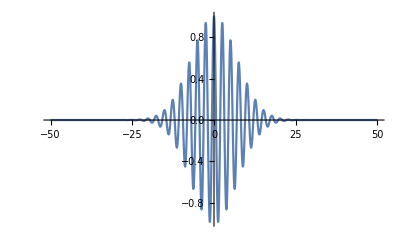

```mathematica
(*Unit definitions*)
n = 10^6;
p = 10^3;
f=10^0;
lambda=760 n;
omega[lam_]:= 2*Pi*(3*10^8/lam);
tp=7f; (*Pulse width*)

w=omega[lambda];
e[t_]:=Exp[-I w t]Exp[-(t/tp)^2/2]
Plot[Re[e[t]],{t,-0.05p,0.05p},PlotRange->All]
```

```mathematica
ifac[td_]:=NIntegrate[Abs[(e[t]+e[t-td])^2]^2,{t,-0.025p,0.025p} ,AccuracyGoal->5]
```

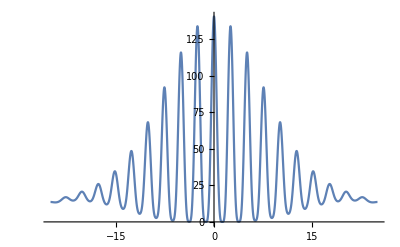

```mathematica
Plot[ifac[td],{td,-25f,25f},PlotRange->All]
```

```mathematica
ifac[0]/ifac[40f]
```

8.00852

3-wavelength IFAC

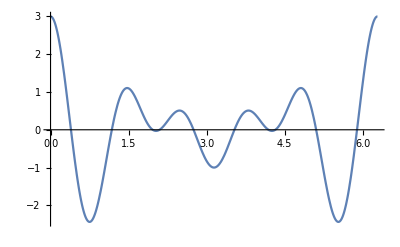

```mathematica
(*Pick 3 frequencies*)
lambda1=600n;
lambda2=700n;
lambda3=800n;
w1=3;
w2=4;
w3=5;
(*Define the 3-frequency electric field*)
e3[t_,phi1_,phi2_,phi3_]:=(Exp[-I (w1 t+phi1)]+Exp[-I (w2 t+phi2)]+Exp[-I (w3 t+phi3)])(* *Exp[-(t/tp)^2/2] *)
(*E-field plot*)
Plot[Re[e3[t,0,0,0]],{t,0,2 Pi },PlotRange->All]
```

```mathematica
if3[td_,phi1_,phi2_,phi3_]:=Integrate[Abs[(e3[t,phi1,phi2,phi3]+e3[t-td,phi1,phi2,phi3])^2]^2,{t,0,2Pi}]
```

```mathematica
if3[td,phi1,phi2,phi3]
```

4 ⅇ^(4 Im[phi1+phi2+phi3]) π (33+4 Cos[phi1-2 phi2+phi3]+2 Cos[phi1-2 phi2+phi3-8 td]+2 Cos[phi1-2 phi2+phi3-5 td]+4 Cos[phi1-2 phi2+phi3-4 td]+2 Cos[phi1-2 phi2+phi3-3 td]+4 Cos[phi1-2 phi2+phi3-td]+8 Cos[td]+4 Cos[2 td]+20 Cos[3 td]+20 Cos[4 td]+20 Cos[5 td]+Cos[6 td]+4 Cos[7 td]+5 Cos[8 td]+4 Cos[9 td]+Cos[10 td]+4 Cos[phi1-2 phi2+phi3+td]+2 Cos[phi1-2 phi2+phi3+3 td]+4 Cos[phi1-2 phi2+phi3+4 td]+2 Cos[phi1-2 phi2+phi3+5 td]+2 Cos[phi1-2 phi2+phi3+8 td])

```mathematica
if3x[td_,phi1_,phi2_,phi3_]:=(33+4 Cos[phi1-2 phi2+phi3]+2 Cos[phi1-2 phi2+phi3-8 td]+2 Cos[phi1-2 phi2+phi3-5 td]+4 Cos[phi1-2 phi2+phi3-4 td]+2 Cos[phi1-2 phi2+phi3-3 td]+4 Cos[phi1-2 phi2+phi3-td]+8 Cos[td]+4 Cos[2 td]+20 Cos[3 td]+20 Cos[4 td]+20 Cos[5 td]+Cos[6 td]+4 Cos[7 td]+5 Cos[8 td]+4 Cos[9 td]+Cos[10 td]+4 Cos[phi1-2 phi2+phi3+td]+2 Cos[phi1-2 phi2+phi3+3 td]+4 Cos[phi1-2 phi2+phi3+4 td]+2 Cos[phi1-2 phi2+phi3+5 td]+2 Cos[phi1-2 phi2+phi3+8 td])
```

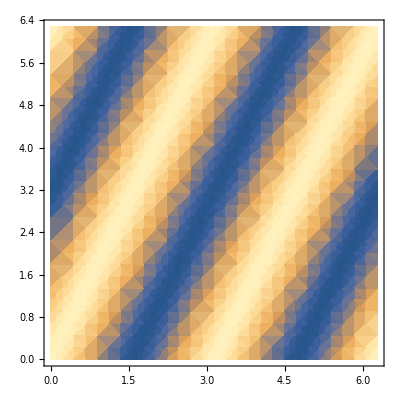

```mathematica
DensityPlot[if3x[0,0,phi2,phi3],{phi2,0,2Pi},{phi3,0,2Pi}]
```

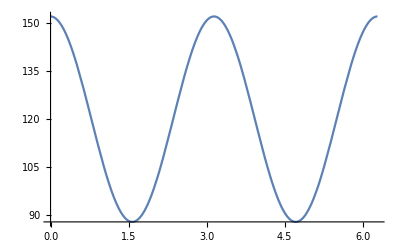

```mathematica
Plot[if3x[0,0,phi2,0],{phi2,0,2Pi}]
```